# Bloch's Sphere

```mathematica
sphere=SphericalPlot3D[1,{θ,0,Pi},{ϕ,0,2 Pi},PlotStyle->{Yellow,Opacity[0.1]},Mesh->None,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Show[sphere,Plot[x^2,{x,-5,5}]]
```

PlotRange::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
generatePointOnSurface[θ_, ϕ_]:={Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ],Cos[θ]}
```

```mathematica
Table[Show[sphere,Graphics3D[{Red,Arrow[{{0,0,0},generatePointOnSurface[j,i]}]}]],{i,0,2π,1},{j,0,π,1}]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
ListAnimate[Flatten@Table[Show[sphere,Graphics3D[{Red,Arrow[{{0,0,0},generatePointOnSurface[j,i]}]}]],{i,0,2π,1},{j,0,π,1}]]
```

```mathematica
Table[Show[sphere,Graphics3D[{Red,Arrow[{{0,0,0},generatePointOnSurface[j,0]}]}]],{j,0,π/2,0.5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[Flatten@Table[Show[sphere,Graphics3D[{Red,Arrow[Tube[{{0,0,0},generatePointOnSurface[j,0]}]]}]],{j,π/2,π,0.05}]]
```

```mathematica
ListAnimate[Flatten@Table[Show[sphere,Graphics3D[{Red,Arrow[Tube[{{0,0,0},generatePointOnSurface[Pi/2,i]}]]}]],{i,0,2π,0.05}]]
```

```mathematica
ListAnimate[Flatten@Table[Show[sphere,Graphics3D[{Red,Arrow[Tube[{{0,0,0},generatePointOnSurface[j,0]}]]}]],{j,π/2,Pi,0.05}]]
```

```mathematica
PrecessTime[ϕ_]:=
ListAnimate[
Flatten@Join[
    Table[Show[sphere,Graphics3D[{Red,GeometricTransformation[Arrow[Tube[{{0,0,0},generatePointOnSurface[0,0]}]],RotationTransform[k Pi/2,{0,1,0}]]}]],{k,0,1,0.1}],
    Table[Show[sphere,Graphics3D[{Red,Point@@{Table[generatePointOnSurface[Pi/2,i],{i,0,ϕ,0.01}]},Arrow[Tube[{{0,0,0},generatePointOnSurface[Pi/2,i]}]]}]],{i,0,ϕ,0.1}],
    Table[Show[sphere,Graphics3D[{Red,GeometricTransformation[Arrow[Tube[{{0,0,0},generatePointOnSurface[π/2,ϕ]}]],RotationTransform[k Pi/2,{0,1,0}]]}]],{k,0,1,0.1}]
            ]
           ]
FinalCoordinate[ϕ_]:=generatePointOnSurface[Pi/2,ϕ].RotationMatrix[Pi/2,{0,1,0}]

GroundStateProb[ϕ_]:=Cos[0.5*CoordinateTransformData["Cartesian"->"Spherical","Mapping",FinalCoordinate[ϕ]][[2]]]^2

Manipulate[PrecessTime[ϕ],{ϕ,0,2Pi,0.5}]

ListAnimate[Table[ListPlot[{Table[{ϕ,GroundStateProb[ϕ]},{ϕ,0.1,θ,0.5}]},PlotRange->{{0,5Pi},{0,1}},AxesLabel->{"ΔT","P_g"}],{θ,0.1,5Pi,0.5}]]
```

```mathematica
Manipulate[PrecessTime[ϕ],{ϕ,0,2Pi,0.5}]
```

```mathematica
ListAnimate[Table[ListPlot[{Table[{ϕ,GroundStateProb[ϕ]},{ϕ,0.1,θ,0.5}]},PlotRange->{{0,5Pi},{0,1}},AxesLabel->{"ΔT","P_g"}],{θ,0.1,5Pi,0.5}]]
```

```mathematica
Show[sphere,Graphics3D[{Red,Arrow[Tube[{{0,0,0},generatePointOnSurface[0,0]}]]}]]
```

-Graphics3D-

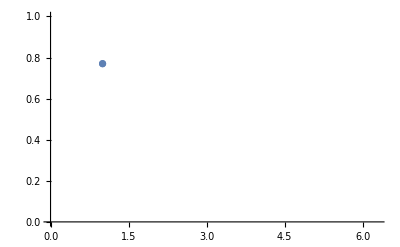
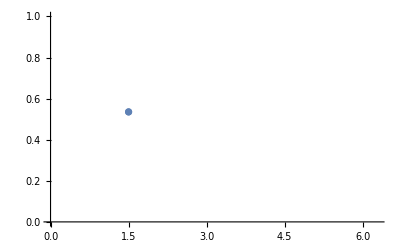
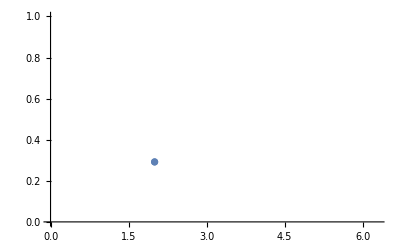
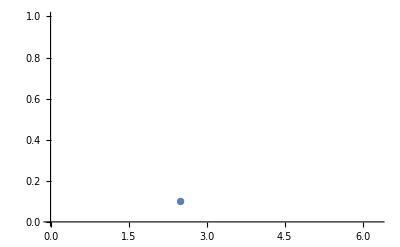
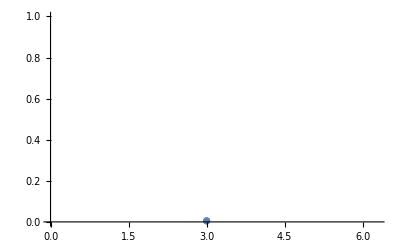
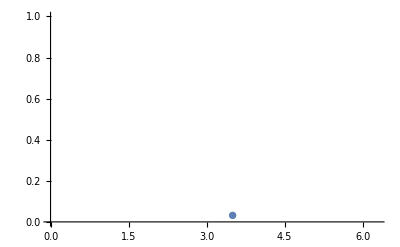
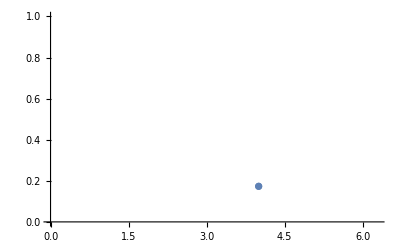
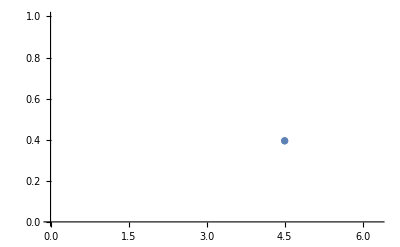

```mathematica
ListPlot[{Table[{ϕ,GroundStateProb[ϕ]},{ϕ,1,2Pi,0.5}]},PlotRange->{{0,2Pi},{0,1}}],{ϕ,1,2Pi,0.5}
```

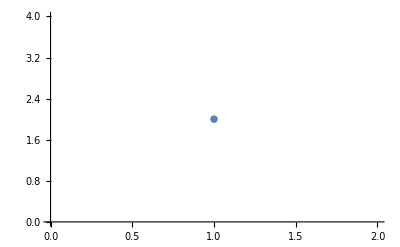

```mathematica
ListPlot[{{1,2}}]
```

```mathematica
Graphics[Point[Table[GroundStateProb[ϕ],{ϕ,0.01,2Pi,0.5}]]]
```

-Graphics-

```mathematica
RotationMatrix[Pi/2,{0,1,0}]//MatrixForm
```

(0 | 0 | 1
0 | 1 | 0
-1 | 0 | 0)

```mathematica
FinalCoordinate[ϕ_]:=generatePointOnSurface[Pi/2,ϕ].RotationMatrix[Pi/2,{0,1,0}]
```

```mathematica
FinalCoordinate[Pi/3]
```

{0,(√3)/2,1/2}

```mathematica
CoordinateTransformData["Cartesian"->"Spherical","Mapping",FinalCoordinate[Pi/2]]
```

{1,π/2,π/2}

```mathematica
{√2,π/2,π/4}[[2]]
```

√2

```mathematica
GroundStateProb[ϕ_]:=Cos[0.5*CoordinateTransformData["Cartesian"->"Spherical","Mapping",FinalCoordinate[ϕ]][[2]]]^2
```

```mathematica
GroundStateProb[7Pi/4]
```

0.853553

```mathematica
Table[GroundStateProb[θ],{θ,-5Pi,5Pi,0.5}]
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

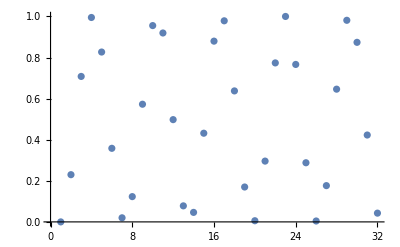

```mathematica
ListPlot[Table[GroundStateProb[θ],{θ,-5Pi,5Pi,1}]]
```

```mathematica
PrecessTime[Pi]
```

```mathematica
ListAnimate[Show[sphere,Graphics3D[Point@@{Table[generatePointOnSurface[j,0],{j,0,π,0.02}]}]]]
```

ListAnimate[-Graphics3D-]

```mathematica
ListAnimate[Table[Show[sphere,Graphics3D[Point@@{generatePointOnSurface[j,0]}]],{j,0,π,0.5}]]
```

```mathematica
Graphics3D[Point@@{Table[generatePointOnSurface[j,0],{j,0,π,0.2}]}]
```

-Graphics3D-

```mathematica
Table[Show[sphere,Graphics3D[{Red,GeometricTransformation[Arrow[Tube[{{0,0,0},generatePointOnSurface[π/2,x]}]],RotationTransform[k Pi/2,{0,1,0}]]}]],{k,0,1,0.2}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Animate[Show[sphere,Graphics3D[{Red,GeometricTransformation[Arrow[Tube[{{0,0,0},generatePointOnSurface[0,0]}]],RotationTransform[k Pi/2,{1,0,0}]]}]],{k,0,1}]
```

```mathematica
Animate[Show[sphere,Graphics3D[{Red,GeometricTransformation[Arrow[Tube[{{0,0,0},generatePointOnSurface[Pi/2,-Pi/2]}]],RotationTransform[k Pi,{0,0,1}]]}]],{k,0,1}]
```

```mathematica
L
```